### Supervised Learning: Classification

Using Classify[] function for classification - Example 1

```mathematica
trainingSet = {1->"A", 2->"A", 3.5->"B", 4->"B"}
```

{1→A,2→A,3.5→B,4→B}

```mathematica
cf = Classify[trainingSet]
```

ClassifierFunction[…]

```mathematica
cf[1.2]
```

A

```mathematica
cf[1.2, "Probabilities"]
```

<|A→1.,B→1.71699×10^-36|>

Using Classify[] function for classification - Example 2

```mathematica
dayNight = Classify[
{-Graphics-->"day",-Graphics-->"day",-Graphics-->"day",-Graphics-->"day",-Graphics-->"night",-Graphics-->"night",-Graphics-->"night",-Graphics-->"night"}]
```

ClassifierFunction[…]

```mathematica
dayNight[{-Graphics-,-Graphics-}]
```

{night,day}

Using Classify[] function for classification - Example 3

```mathematica
coloredPoints = {{0.964,0.729}->Red,{0.341,0.572}->Blue,{0.915,0.024}->Red,{0.674,0.211}->Red,{0.62,0.64}->Green,{0.573,0.245}->Red,
			     {0.985,0.014}->Red,{0.432,0.373}->Red,{0.407,0.148}->Red,{0.646,0.982}->Green,{0.99,0.621}->Red,{0.206,0.843}->Green,
			     {0.133,0.778}->Blue,{0.135,0.787}->Blue,{0.897,0.282}->Green,{0.516,0.963}->Green,{0.071,0.859}->Blue,
			    {0.25,0.444}->Blue,{0.721,0.97}->Green,{0.641,0.324}->Green}
```

{{0.964,0.729}→RGBColor[1, 0, 0],{0.341,0.572}→RGBColor[0, 0, 1],{0.915,0.024}→RGBColor[1, 0, 0],{0.674,0.211}→RGBColor[1, 0, 0],{0.62,0.64}→RGBColor[0, 1, 0],{0.573,0.245}→RGBColor[1, 0, 0],{0.985,0.014}→RGBColor[1, 0, 0],{0.432,0.373}→RGBColor[1, 0, 0],{0.407,0.148}→RGBColor[1, 0, 0],{0.646,0.982}→RGBColor[0, 1, 0],{0.99,0.621}→RGBColor[1, 0, 0],{0.206,0.843}→RGBColor[0, 1, 0],{0.133,0.778}→RGBColor[0, 0, 1],{0.135,0.787}→RGBColor[0, 0, 1],{0.897,0.282}→RGBColor[0, 1, 0],{0.516,0.963}→RGBColor[0, 1, 0],{0.071,0.859}→RGBColor[0, 0, 1],{0.25,0.444}→RGBColor[0, 0, 1],{0.721,0.97}→RGBColor[0, 1, 0],{0.641,0.324}→RGBColor[0, 1, 0]}

```mathematica
cpc=Classify[coloredPoints, Method->Automatic]
```

ClassifierFunction[…]

```mathematica
cpc[{1,1}]
```

RGBColor[0, 1, 0]

Using Classify[] function for classification - Example 4

```mathematica
irisData = ExampleData[{"MachineLearning","FisherIris"},"Data"]
```

{{5.1,3.5,1.4,0.2}→setosa,{4.9,3.,1.4,0.2}→setosa,{4.7,3.2,1.3,0.2}→setosa,{4.6,3.1,1.5,0.2}→setosa,{5.,3.6,1.4,0.2}→setosa,{5.4,3.9,1.7,0.4}→setosa,{4.6,3.4,1.4,0.3}→setosa,{5.,3.4,1.5,0.2}→setosa,{4.4,2.9,1.4,0.2}→setosa,{4.9,3.1,1.5,0.1}→setosa,{5.4,3.7,1.5,0.2}→setosa,{4.8,3.4,1.6,0.2}→setosa,{4.8,3.,1.4,0.1}→setosa,{4.3,3.,1.1,0.1}→setosa,{5.8,4.,1.2,0.2}→setosa,{5.7,4.4,1.5,0.4}→setosa,{5.4,3.9,1.3,0.4}→setosa,{5.1,3.5,1.4,0.3}→setosa,{5.7,3.8,1.7,0.3}→setosa,{5.1,3.8,1.5,0.3}→setosa,{5.4,3.4,1.7,0.2}→setosa,{5.1,3.7,1.5,0.4}→setosa,{4.6,3.6,1.,0.2}→setosa,{5.1,3.3,1.7,0.5}→setosa,{4.8,3.4,1.9,0.2}→setosa,{5.,3.,1.6,0.2}→setosa,{5.,3.4,1.6,0.4}→setosa,{5.2,3.5,1.5,0.2}→setosa,{5.2,3.4,1.4,0.2}→setosa,{4.7,3.2,1.6,0.2}→setosa,{4.8,3.1,1.6,0.2}→setosa,{5.4,3.4,1.5,0.4}→setosa,{5.2,4.1,1.5,0.1}→setosa,{5.5,4.2,1.4,0.2}→setosa,{4.9,3.1,1.5,0.2}→setosa,{5.,3.2,1.2,0.2}→setosa,{5.5,3.5,1.3,0.2}→setosa,{4.9,3.6,1.4,0.1}→setosa,{4.4,3.,1.3,0.2}→setosa,{5.1,3.4,1.5,0.2}→setosa,{5.,3.5,1.3,0.3}→setosa,{4.5,2.3,1.3,0.3}→setosa,{4.4,3.2,1.3,0.2}→setosa,{5.,3.5,1.6,0.6}→setosa,{5.1,3.8,1.9,0.4}→setosa,{4.8,3.,1.4,0.3}→setosa,{5.1,3.8,1.6,0.2}→setosa,{4.6,3.2,1.4,0.2}→setosa,{5.3,3.7,1.5,0.2}→setosa,{5.,3.3,1.4,0.2}→setosa,{7.,3.2,4.7,1.4}→versicolor,{6.4,3.2,4.5,1.5}→versicolor,{6.9,3.1,4.9,1.5}→versicolor,{5.5,2.3,4.,1.3}→versicolor,{6.5,2.8,4.6,1.5}→versicolor,{5.7,2.8,4.5,1.3}→versicolor,{6.3,3.3,4.7,1.6}→versicolor,{4.9,2.4,3.3,1.}→versicolor,{6.6,2.9,4.6,1.3}→versicolor,{5.2,2.7,3.9,1.4}→versicolor,{5.,2.,3.5,1.}→versicolor,{5.9,3.,4.2,1.5}→versicolor,{6.,2.2,4.,1.}→versicolor,{6.1,2.9,4.7,1.4}→versicolor,{5.6,2.9,3.6,1.3}→versicolor,{6.7,3.1,4.4,1.4}→versicolor,{5.6,3.,4.5,1.5}→versicolor,{5.8,2.7,4.1,1.}→versicolor,{6.2,2.2,4.5,1.5}→versicolor,{5.6,2.5,3.9,1.1}→versicolor,{5.9,3.2,4.8,1.8}→versicolor,{6.1,2.8,4.,1.3}→versicolor,{6.3,2.5,4.9,1.5}→versicolor,{6.1,2.8,4.7,1.2}→versicolor,{6.4,2.9,4.3,1.3}→versicolor,{6.6,3.,4.4,1.4}→versicolor,{6.8,2.8,4.8,1.4}→versicolor,{6.7,3.,5.,1.7}→versicolor,{6.,2.9,4.5,1.5}→versicolor,{5.7,2.6,3.5,1.}→versicolor,{5.5,2.4,3.8,1.1}→versicolor,{5.5,2.4,3.7,1.}→versicolor,{5.8,2.7,3.9,1.2}→versicolor,{6.,2.7,5.1,1.6}→versicolor,{5.4,3.,4.5,1.5}→versicolor,{6.,3.4,4.5,1.6}→versicolor,{6.7,3.1,4.7,1.5}→versicolor,{6.3,2.3,4.4,1.3}→versicolor,{5.6,3.,4.1,1.3}→versicolor,{5.5,2.5,4.,1.3}→versicolor,{5.5,2.6,4.4,1.2}→versicolor,{6.1,3.,4.6,1.4}→versicolor,{5.8,2.6,4.,1.2}→versicolor,{5.,2.3,3.3,1.}→versicolor,{5.6,2.7,4.2,1.3}→versicolor,{5.7,3.,4.2,1.2}→versicolor,{5.7,2.9,4.2,1.3}→versicolor,{6.2,2.9,4.3,1.3}→versicolor,{5.1,2.5,3.,1.1}→versicolor,{5.7,2.8,4.1,1.3}→versicolor,{6.3,3.3,6.,2.5}→virginica,{5.8,2.7,5.1,1.9}→virginica,{7.1,3.,5.9,2.1}→virginica,{6.3,2.9,5.6,1.8}→virginica,{6.5,3.,5.8,2.2}→virginica,{7.6,3.,6.6,2.1}→virginica,{4.9,2.5,4.5,1.7}→virginica,{7.3,2.9,6.3,1.8}→virginica,{6.7,2.5,5.8,1.8}→virginica,{7.2,3.6,6.1,2.5}→virginica,{6.5,3.2,5.1,2.}→virginica,{6.4,2.7,5.3,1.9}→virginica,{6.8,3.,5.5,2.1}→virginica,{5.7,2.5,5.,2.}→virginica,{5.8,2.8,5.1,2.4}→virginica,{6.4,3.2,5.3,2.3}→virginica,{6.5,3.,5.5,1.8}→virginica,{7.7,3.8,6.7,2.2}→virginica,{7.7,2.6,6.9,2.3}→virginica,{6.,2.2,5.,1.5}→virginica,{6.9,3.2,5.7,2.3}→virginica,{5.6,2.8,4.9,2.}→virginica,{7.7,2.8,6.7,2.}→virginica,{6.3,2.7,4.9,1.8}→virginica,{6.7,3.3,5.7,2.1}→virginica,{7.2,3.2,6.,1.8}→virginica,{6.2,2.8,4.8,1.8}→virginica,{6.1,3.,4.9,1.8}→virginica,{6.4,2.8,5.6,2.1}→virginica,{7.2,3.,5.8,1.6}→virginica,{7.4,2.8,6.1,1.9}→virginica,{7.9,3.8,6.4,2.}→virginica,{6.4,2.8,5.6,2.2}→virginica,{6.3,2.8,5.1,1.5}→virginica,{6.1,2.6,5.6,1.4}→virginica,{7.7,3.,6.1,2.3}→virginica,{6.3,3.4,5.6,2.4}→virginica,{6.4,3.1,5.5,1.8}→virginica,{6.,3.,4.8,1.8}→virginica,{6.9,3.1,5.4,2.1}→virginica,{6.7,3.1,5.6,2.4}→virginica,{6.9,3.1,5.1,2.3}→virginica,{5.8,2.7,5.1,1.9}→virginica,{6.8,3.2,5.9,2.3}→virginica,{6.7,3.3,5.7,2.5}→virginica,{6.7,3.,5.2,2.3}→virginica,{6.3,2.5,5.,1.9}→virginica,{6.5,3.,5.2,2.}→virginica,{6.2,3.4,5.4,2.3}→virginica,{5.9,3.,5.1,1.8}→virginica}

```mathematica
irisTrainingData = RandomSample[irisData, 100];
```

```mathematica
irisTestData = Complement[irisData, irisTrainingData];
```

```mathematica
Intersection[irisTrainingData, irisTestData]
```

{}

```mathematica
irisCf = Classify[irisTrainingData]
```

ClassifierFunction[…]

```mathematica
irisCm = ClassifierMeasurements[irisCf, irisTestData]
```

ClassifierMeasurementsObject[…]

```mathematica
irisCm["Accuracy"]
```

0.979592

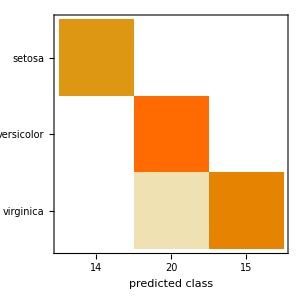

```mathematica
irisCm["ConfusionMatrixPlot"]
```

```mathematica
irisCm["Properties"]
```

{Accuracy,AccuracyRejectionPlot,ClassRejectionRate,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,Error,FScore,InversePerplexity,Likelihood,LogLikelihood,LogLikelihoodRate,Perplexity,Precision,Properties,Recall,RejectionRate}